```mathematica
five=Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&];five=DeleteDuplicates[Join[allGraphs5FakeAtomKeys, allGraphs5GeneratorAtomKeys]];Length[five]
```

102

```mathematica
fiveSorted=Sort[five,Length[ListofVars[allGraphs5[#1,"colofour"]]]>Length[ListofVars[allGraphs5[#2,"colofour"]]]&];Length[fiveSorted]
```

102

```mathematica
fiveEdges=Block[{i,j, main,mainVars, sub,subVars,result={}},
Monitor[
For[i=1,i≤Length[fiveSorted],i++,
main=fiveSorted[[i]];
mainVars=ListofVars[allGraphs5[main,"colofour"]];
For[j=i+1,j≤Length[fiveSorted],j++,
sub=fiveSorted[[j]];
subVars=ListofVars[allGraphs5[sub,"colofour"]];
If[SubSetQ[mainVars,subVars],
AppendTo[result,main->sub]
]
]
],
{i,j,Length[result]}
];
result
];Length[fiveEdges]
```

1661

```mathematica
gCleaned=Block[{g=Graph[fiveEdges],vertices,paths,cleaned=0},
vertices=Sort[VertexList[g]];
Monitor[
Table[
paths=FindPath[g,e[[1]],e[[2]],{2,100}];
If[Length[paths]≠0,
g=EdgeDelete[g,e];
cleaned++
]
,{e,Sort[fiveEdges]}
],
{e,cleaned}
];
Print[cleaned];
g
];
```

1181

```mathematica
EdgeCount[gCleaned]
```

480

```mathematica
Length[fiveEdges]
```

1661

```mathematica
Intersection[VertexList[gCleaned],allGraphs5GeneratorAtomKeys]
```

{0,760,2278,3036,3037,6816,7570,7573,9076,9085,9828,9832,9838,9840,9841,20034,20740,20767,22150,22231,22854,22882,22936,22962,22963,26364,26607,27064,27094,27310,27334,27337,28462,28552,28714,28786,28795,29160,29191,29251,29280,29281,29415,29440,29443,29488,29497,29511,29515,29521,29523,29524}

```mathematica
Select[VertexList[gCleaned],VertexDegree[gCleaned,#]==1&]
```

{}

```mathematica
VertexCount[gCleaned]
```

102

```mathematica
gCleaned2=VertexDelete[gCleaned,Select[VertexList[gCleaned],VertexDegree[gCleaned,#]==1&]];
```

```mathematica
VertexCount[gCleaned2]
```

102

```mathematica
Select[VertexList[gCleaned2],VertexOutDegree[gCleaned2,#]==0&&#≠K5Key&]
```

{}

```mathematica
gCleaned3=VertexDelete[gCleaned2,Select[VertexList[gCleaned2],VertexOutDegree[gCleaned2,#]==0&&#≠K5Key&]];
```

```mathematica
VertexCount[gCleaned3]
```

102

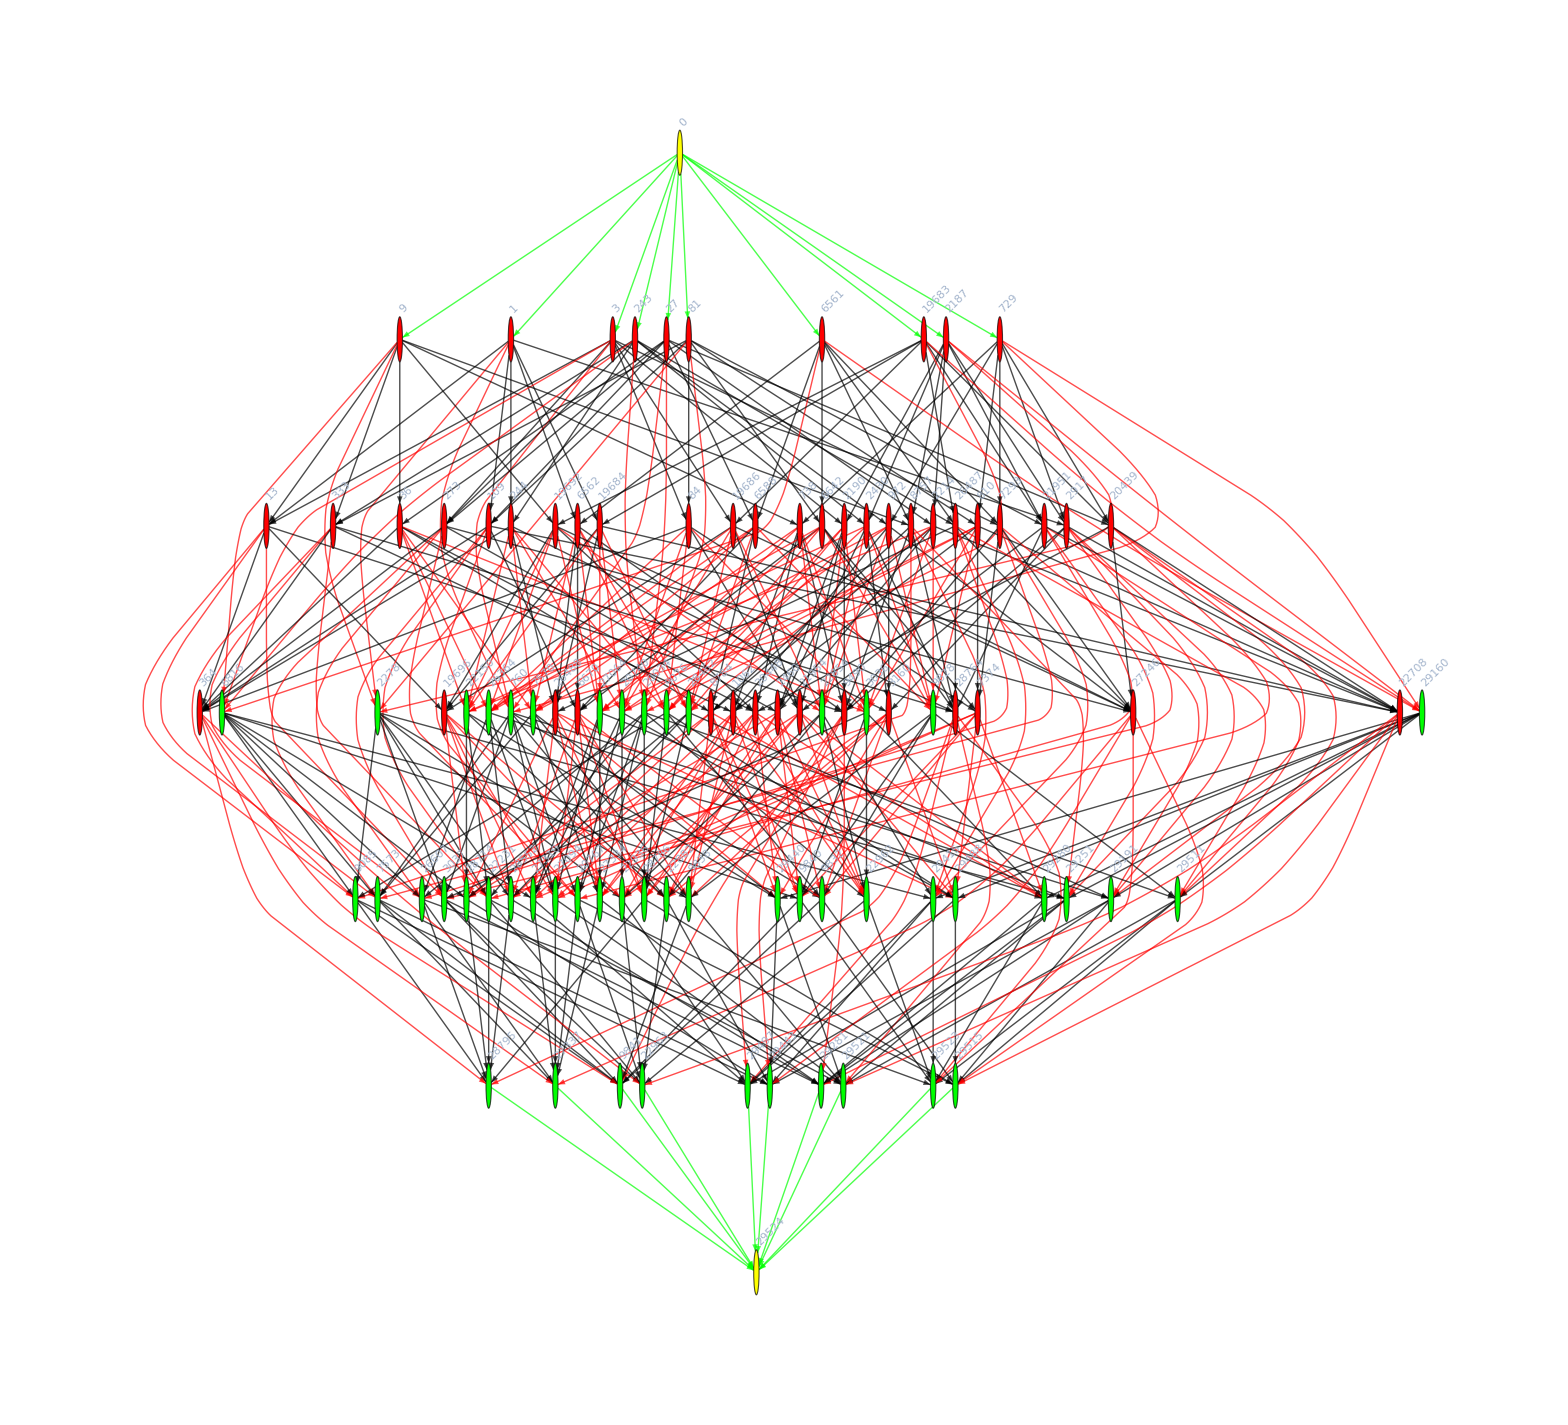

```mathematica
Graph[gCleaned,GraphLayout->"LayeredDigraphEmbedding",VertexLabels->Table[k->Tooltip[Rotate[k,Pi/4],ShowGraph5Least[k]],{k,Keys[allGraphs5]}],
VertexStyle->Table[k->If[MemberQ[allGraphs5FakeAtomKeys,k],If[MemberQ[allGraphs5GeneratorAtomKeys,k],Yellow,Red],Green],{k,Keys[allGraphs5]}],
EdgeStyle->Table[e->If[MemberQ[allGraphs5GeneratorAtomKeys,e [[2]]]&&MemberQ[allGraphs5FakeAtomKeys,e [[1]]],Red,If[MemberQ[allGraphs5GeneratorAtomKeys,e [[1]]]&&MemberQ[allGraphs5FakeAtomKeys,e [[2]]],Green,Black]],{e,EdgeList[gCleaned]}],ImageSize->1800,AspectRatio->1/1.1]
```

```mathematica
IntegerDigits[29524,3]
```

{1,1,1,1,1,1,1,1,1,1}

```mathematica
Table[(n*(n-1)/4)2^(n*(n-1)/2),{n,20}]
```

{0,1,12,192,5120,245760,22020096,3758096384,1236950581248,791648371998720,990791918021509120,2434970217729660813312,11787026741242634453385216,112652543574969605015820304384,2129653008383425394514461385031680,79753679747094952374228423616820674560,5923635443359696771970425166172221025026048,873475587936047447207671013303091023466240933888,255914782703190424589138028947952021873832412005269504,149081166215433668141099998801182077382430941806020819681280}

```mathematica
Tally[Table[allGraphs5[e[[1]],"atleast"]>allGraphs5[e[[2]],"atleast"],{e,EdgeList[gCleaned]}]]
```

{{True,440},{False,40}}

```mathematica
Select[EdgeList[gCleaned],#[[2]]==3&]
```

{0->3}

```mathematica
allGraphs5[0,"atleast"]
```

34

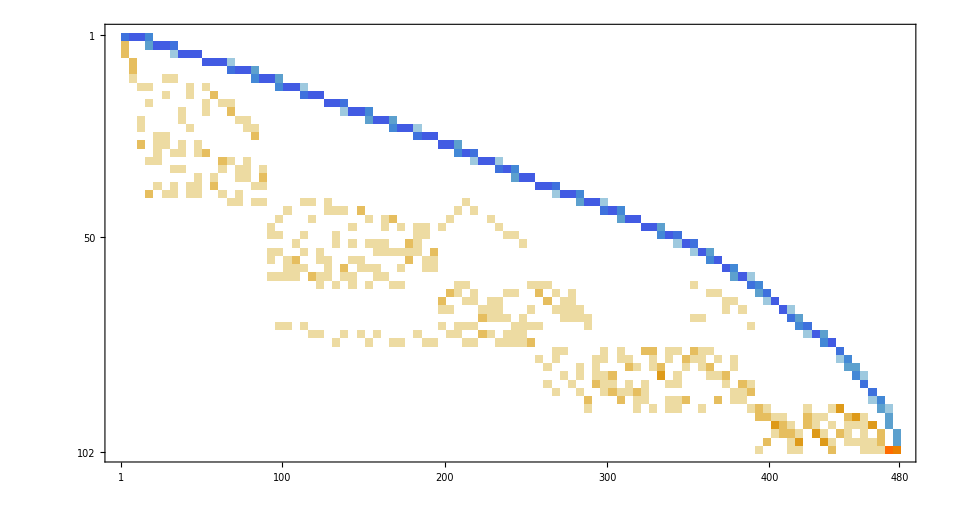

```mathematica
Graph[gCleaned,GraphLayout->"LayeredDigraphEmbedding",VertexLabels->Table[k->Tooltip[Rotate[k,Pi/4],ShowGraph5Least[k]],{k,Keys[allGraphs5]}],
VertexStyle->Table[k->If[MemberQ[allGraphs5FakeAtomKeys,k],If[MemberQ[allGraphs5GeneratorAtomKeys,k],Yellow,Red],Green],{k,Keys[allGraphs5]}],
EdgeStyle->Table[e->If[MemberQ[allGraphs5GeneratorAtomKeys,e [[2]]]&&MemberQ[allGraphs5FakeAtomKeys,e [[1]]],Red,If[MemberQ[allGraphs5GeneratorAtomKeys,e [[1]]]&&MemberQ[allGraphs5FakeAtomKeys,e [[2]]],Green,Black]],{e,EdgeList[gCleaned]}],ImageSize->1800,AspectRatio->1/1.1]//IncidenceMatrix//MatrixPlot
```

```mathematica
FactorInteger[1625183903848807379751696895006957888044060191615970354893197653038175051554010000000000000000000000]
```

{{2,22},{3,140},{5,22},{11,10}}

```mathematica
allGraphs5[364,"colofourgenerator"]
```

g12x3x4x5+g13x2x4x5+g14x2x3x5+g15x2x3x4-3 g1x2x3x4x5

```mathematica
allGraphs5[6816,"colofourgenerator"]
```

g1245x3

```mathematica
allGraphs5[364,"colofournull"]
```

p1x2345

```mathematica
allGraphs5[6816,"colofournull"]
```

1/24 (p12345+3 p1234x5+3 p1235x4-p123x45+6 p123x4x5-p1245x3-p124x35-2 p124x3x5-p125x34-2 p125x3x4-p12x345-2 p12x34x5-2 p12x35x4+2 p12x3x45-2 p12x3x4x5+3 p1345x2-p134x25+6 p134x2x5-p135x24+6 p135x2x4-p13x245-2 p13x24x5-2 p13x25x4-2 p13x2x45+6 p13x2x4x5-p145x23-2 p145x2x3-p14x235-2 p14x23x5+2 p14x25x3-2 p14x2x35-2 p14x2x3x5-p15x234-2 p15x23x4+2 p15x24x3-2 p15x2x34-2 p15x2x3x4+3 p1x2345+6 p1x234x5+6 p1x235x4-2 p1x23x45+6 p1x23x4x5-2 p1x245x3-2 p1x24x35-2 p1x24x3x5-2 p1x25x34-2 p1x25x3x4+6 p1x2x345+6 p1x2x34x5+6 p1x2x35x4-2 p1x2x3x45)